# CBETA Plots

```mathematica
(*Random CBETA plots - hourglass effect + whatever else*)
```

## Cases + Constants

```mathematica
(*Constants*)
Me = 0.511*10^6;
eleccharge=1.6*10^-19;
c = 299792458;
sigT=6.65*10^-29;
```

```mathematica
(*Cases vary laser spot size Subscript[σ, L] and beam size Subscript[σ, e] and are used to plot the flux and bandwidth (both raw and hourglass case*) 
(*scaling of laser spot size*)
scalefac = 2;

CBETA150σL2 = {γ->293.54, Elaser->1.17, ϵn->0.3*10^-6,ϕ->0,σL->25*10^-6*scalefac,Q->32*10^-12,Epulse->62*10^-6,rep->1.3*10^9,tpulse->10*10^-12,σz->1*10^-3,θcol->0.5*10^-3,EbSpread->3*10^-4,ELSpread->6.57*10^-4};
CBETA150σL = {γ->293.54, Elaser->1.17, ϵn->0.3*10^-6,ϕ->0,σL->25*10^-6,Q->32*10^-12,Epulse->62*10^-6,rep->1.3*10^9,tpulse->10*10^-12,σz->1*10^-3,θcol->0.5*10^-3,EbSpread->3*10^-4,ELSpread->6.57*10^-4};
CBETA150σLhalf = {γ->293.54, Elaser->1.17, ϵn->0.3*10^-6,ϕ->0,σL->25*10^-6*(1/scalefac),Q->32*10^-12,Epulse->62*10^-6,rep->1.3*10^9,tpulse->10*10^-12,σz->1*10^-3,θcol->0.5*10^-3,EbSpread->3*10^-4,ELSpread->6.57*10^-4};
```

```mathematica
trialcase = CBETA150σL2;
```

# Hourglass Effect

## Sub Equations

```mathematica
(*Recoil Parameter*)
Xrec[γ_,Einc_]:=(4*γ*Einc)/Me;

(*ψ from θ*)
ψ[θ_,γ_]:=γ*θ;

(*Compton Cross Section*)
σc[γ_,Einc_]:=sigT*(1-Xrec[γ,Einc]);

(*No. Electrons*)
Ne[Q_]:=Q/eleccharge;
(*No. Photons*)
NL[Epulse_,Einc_]:=Epulse/(Einc*eleccharge);
βIP[σe_,γ_,ϵn_]:=(σe^2*γ)/ϵn;
convl[σz_,tpulse_]:=Sqrt[σz^2+(c*tpulse)^2];
conv[σe_,σL_]:=Sqrt[σe^2+σL^2];
(*Raw Flux Value*)
F[rep_,Q_,Epulse_,σL_,γ_,σe_,Einc_,ϕ_,σz_,tpulse_]:=σc[γ,Einc]*(rep*Ne[Q]*NL[Epulse,Einc]*Cos[ϕ/2])/(2*π*conv[σL,σe]*Sqrt[conv[σL,σe]^2*Cos[ϕ/2]^2+convl[σz,tpulse]^2*Sin[ϕ/2]^2]);
(*Bandwidth Calc*)
collterm[θcol_,γ_,Einc_]:=ψ[γ,θcol]^2/(Sqrt[12]*(1+Xrec[γ,Einc]+(ψ[γ,θcol]^2/2)));
beamEterm[θcol_,γ_,Einc_,EbSpread_]:=(2+Xrec[γ,Einc])/(1+Xrec[γ,Einc]+ψ[γ,θcol]^2)*EbSpread;
laserEterm[θcol_,γ_,Einc_,ELSpread_]:=(1+ψ[γ,θcol]^2)/(1+Xrec[γ,Einc]+ψ[γ,θcol]^2)*ELSpread;
emitterm[γ_,ϵn_,σe_]:=Sqrt[(2*γ*ϵn)/βIP[σe,γ,ϵn]];
BW[θcol_,γ_,Einc_,EbSpread_,ELSpread_,ϵn_,σe_]:=Sqrt[collterm[θcol,γ,Einc]^2+beamEterm[θcol,γ,Einc,EbSpread]^2+laserEterm[θcol,γ,Einc,ELSpread]^2+emitterm[γ,ϵn,σe]^2];
```

## t Parameter + Contribution

```mathematica
(*calculation of t values*)
(*We assume t- and t+ are the beam and laser respectively*)
(*what is Subscript[σ, s] and Subscript[σ, x] - think this is the point slightly down the bunch i.e the head/tail spot size??*)
(*what is the laser β*?? I'm guessing that t is the bunch duration??*)
(*w(z)=w0*Sqrt[1+(z/zR)^2] gives the laser spot size further in z z=s*)
(*σLs2 :=;
σes2:=σe^2
tx2[σL_,σe_]:=(2*(σL^2+σe^2))/□*)
```

## Plots of F, BW, Avg Brill vs σe (varying fixed σL)(non-hourglass)

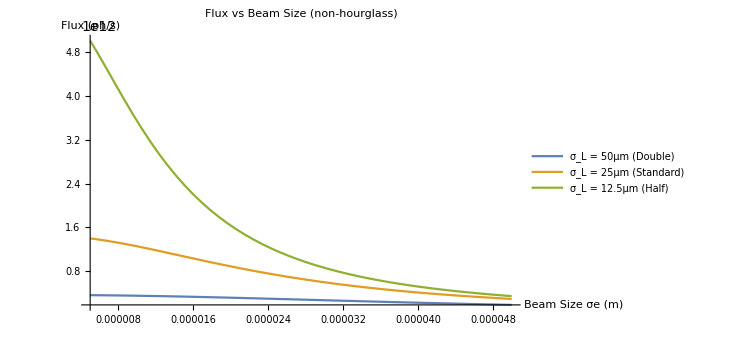

```mathematica
(*Basically going to establish a range for σe: 5μm <σe< 50μm, then trial this at σL/2 , σL, 2σL + plot these values for the flux and the bandwidth*)
(*Use σe as a parameter - makes plotting easier + can work back from this to get β* for bandwidth*) 

(*Flux Plot*)
Plot[{F[rep,Q,Epulse,σL,γ,σe,Elaser,ϕ,σz,tpulse]/.CBETA150σL2,F[rep,Q,Epulse,σL,γ,σe,Elaser,ϕ,σz,tpulse]/.CBETA150σL,F[rep,Q,Epulse,σL,γ,σe,Elaser,ϕ,σz,tpulse]/.CBETA150σLhalf},{σe,5*10^-6,50*10^-6},GridLines->{{25*10^-6},{}},PlotLabel->"Flux vs Beam Size (non-hourglass)",AxesLabel->{"Beam Size σe (m)","Flux (ph/s)"},PlotRange->All ,PlotLegends->Placed[{"σ_L = 50μm (Double)","σ_L = 25μm (Standard)", "σ_L = 12.5μm (Half)"},{0.8,0.65}]]
```

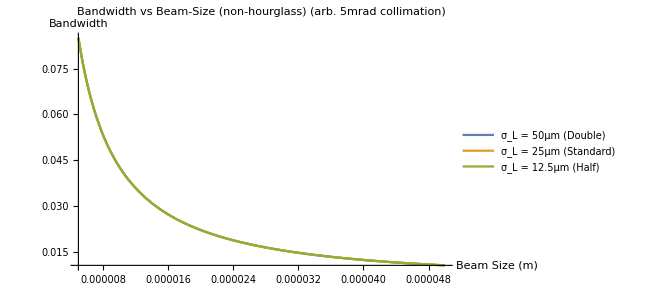

```mathematica
(*Bandwidth Plot*)
Plot[{BW[θcol,γ,Elaser,EbSpread,ELSpread,ϵn,σe]/.CBETA150σL2,BW[θcol,γ,Elaser,EbSpread,ELSpread,ϵn,σe]/.CBETA150σL,BW[θcol,γ,Elaser,EbSpread,ELSpread,ϵn,σe]/.CBETA150σLhalf},{σe,5*10^-6,50*10^-6},GridLines->{{25*10^-6},{}},PlotLabel->"Bandwidth vs Beam-Size (non-hourglass) (arb. 5mrad collimation)",AxesLabel->{"Beam Size (m)","Bandwidth "},PlotRange->All,PlotLegends->Placed[{"σ_L = 50μm (Double)","σ_L = 25μm (Standard)", "σ_L = 12.5μm (Half)"},{0.8,0.65}]]
```

```mathematica
(*Avg Brilliance Plot has the same dependency as the flux and therefore it is not shown here! i.e the only beam size and laser size contribution in this case comes from the flux*)
```

## β-θ CBETA Optimisation Plots

```mathematica
(*Uses the data from the FixedBandwidthOptExtendedFIX script*)
```

```mathematica
(*Using multiple cases to create β-θ Maximum plots*)
SetDirectory[NotebookDirectory[]];
CBETAβθ150=<<"caseCBETA150BetaTheta.txt";
CBETAβθ114=<<"caseCBETA114BetaTheta.txt";
CBETAβθ078=<<"caseCBETA078BetaTheta.txt";
CBETAβθ042=<<"caseCBETA042BetaTheta.txt";
```

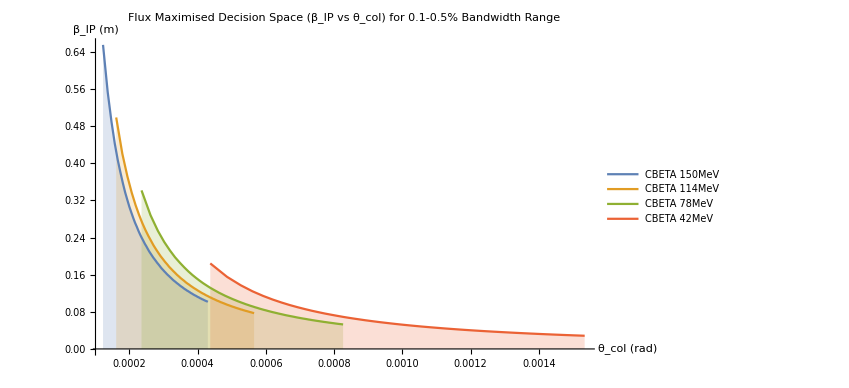

```mathematica
(*β-θ Plot*)
ListLinePlot[{Transpose[CBETAβθ150],Transpose[CBETAβθ114],Transpose[CBETAβθ078],Transpose[CBETAβθ042]},AxesLabel->{"θ_col (rad)","β_IP (m)"},PlotLabel->"Flux Maximised Parameter Space (β_IP vs θ_col) for 0.1-0.5% Bandwidth Range",PlotLegends->Placed[{"CBETA 150MeV","CBETA 114MeV","CBETA 78MeV","CBETA 42MeV"},{0.8,0.6}],PlotRange->All,Filling->Axis]
```

```mathematica
(*Using multiples cases to create F-BW Maximum Plots*)
SetDirectory[NotebookDirectory[]];
CBETAFBW150=<< "caseCBETA150FBW.txt";
CBETAFBW114=<< "caseCBETA114FBW.txt";
CBETAFBW078=<< "caseCBETA078FBW.txt";
CBETAFBW042=<< "caseCBETA042FBW.txt";
```

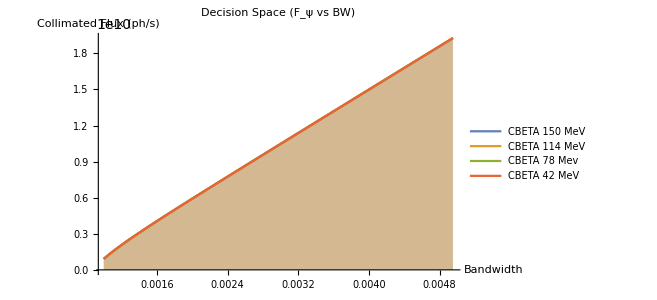

```mathematica
(*F-BW Plot*)
ListLinePlot[{Transpose[CBETAFBW150],Transpose[CBETAFBW114],Transpose[CBETAFBW078],Transpose[CBETAFBW042]},PlotLabel->"Decision Space (F_ψ vs BW)",AxesLabel->{"Bandwidth","Collimated Flux (ph/s)"},PlotLegends->Placed[{"CBETA 150 MeV","CBETA 114 MeV", "CBETA 78 Mev", "CBETA 42 MeV"},{0.85,0.4}],Filling->Axis]
```